# ShiFei

ShiFei(-1 | 1 | 1 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 1
1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 1 | -1 | 1 | 0
0 | 0 | 0 | 1 | -1 | -1) has rank 3 and deficiency δ=N-L-S=6-2-3=1  variables {c_C0,c_S1,c_C1,c_S2,c_C2} cons {C_0+C_1+C_2,C_1+2 C_2+S_1+S_2}

5 variables={c_C0,c_S1,c_C1,c_S2,c_C2}={C_0,S_1,C_1,S_2,C_2}{5}

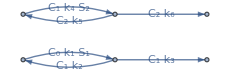

PTM cycle of Shinar, ...{C0+S1→C1,C1→C0+S1,C1→C0+S2,C1+S2→C2,C2→C1+S2,C2→C1+S1} has 6 reactions ,S mat=(-1 | 1 | 1 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 1
1 | -1 | -1 | -1 | 1 | 1
0 | 0 | 1 | -1 | 1 | 0
0 | 0 | 0 | 1 | -1 | -1) conservations (C_0+C_1+C_2
C_1+2 C_2+S_1+S_2) and gen (1 | 1 | 0
0 | 1 | 0
1 | 0 | 0
1 | 0 | 1
0 | 0 | 1
1 | 0 | 0) IaHJF inc. matrix  | C0+S1→C1 | C1→C0+S1 | C1→C0+S2 | C1+S2→C2 | C2→C1+S2 | C2→C1+S1
C0+S1 | -1 | 1 | 0 | 0 | 0 | 0
C1 | 1 | -1 | -1 | 0 | 0 | 0
C0+S2 | 0 | 0 | 1 | 0 | 0 | 0
C1+S2 | 0 | 0 | 0 | -1 | 1 | 0
C2 | 0 | 0 | 0 | 1 | -1 | -1
C1+S1 | 0 | 0 | 0 | 0 | 0 | 1 comp matrix (1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0)  and RHS= (C_1 (k_2+k_3)-C_0 k_1 S_1
C_1 k_2+C_2 k_6-C_0 k_1 S_1
C_2 (k_5+k_6)+C_0 k_1 S_1-C_1 (k_2+k_3+k_4 S_2)
C_2 k_5+C_1 (k_3-k_4 S_2)
-C_2 (k_5+k_6)+C_1 k_4 S_2)

{}

check for cycles(-1 | 0 | 0
0 | 0 | 0
1 | 0 | 0
-1 | 0 | 0
0 | 0 | 0
1 | 0 | 0) so 2 cycles

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C_0→0,C_1→0,C_2→0},{S_1→0,C_1→0,C_2→0},{S_1→(C_1 (k_2+k_3))/(C_0 k_1),S_2→(k_3 (k_5+k_6))/(k_4 k_6),C_2→(C_1 k_3)/k_6}}

{0,0,0,0,0}

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];AppendTo[$Path,"C:\\Users\\flori\\Dropbox\\Codes"];
<<EpidCRN.wl;(*?EpidCRN`**)
Needs["ReactionKinetics`"];(*Names["EpidCRN`*"],Names["ReactionKinetics`*"];Information["ReactionsData"]*)

Format[x1]:=Subscript[x,1];Format[x2]:=Subscript[x,2];
Format[x3]:=Subscript[x,3];Format[R1]:=Subscript[R,1];Format[k1]:=Subscript[k,1];Format[k2]:=Subscript[k,2];
Format[k3]:=Subscript[k,3];Format[k4]:=Subscript[k,4];Format[k5]:=Subscript[k,5];
Format[k6]:=Subscript[k,6];Format[R1m]:=Subscript[R,-1];Format[S1]:=Subscript[S,1];Format[S2]:=Subscript[S,2];
Format[C1]:=Subscript[C,1];Format[C0]:=Subscript[C,0];Format[C2]:=Subscript[C,2];
Format[R2]:=Subscript[R,2];
Format[R3]:=Subscript[R,3];Format[R3m]:=Subscript[R,-3];Format[R4]:=Subscript[R,4];

c23={ S1->0,  C0->0};c35={C1->0,  C0->0};
c135={ C0->0,  C0->0,C1->0};cACR= S2->(k3 (k5+k6))/(k4  k6);cDFE={ S1->0,C1->0,  C2->0};
RN={"S1"+"C0"->"C1","C1"->"C0"+"S1","C1"->"S2"+"C0","S2"+"C1" ->"C2" ,"C2"->"S2"+"C1", "C2"->"S1"+"C1"};
var={ C0,  S1,  C1, S2,C2};
RND=ReactionsData[RN];Γ=RND["γ"]//Normal;fl=cons[Γ//Transpose]//Transpose;
expo= RND["α"]//Normal//Transpose;con=cons[Γ];conx=con.var;
{comp,r,nR,spec,nS,vol,vars,defi}=RND["complexes","reactionsteps","R","species","M","volpertgraph","variables","deficiency"];
Print[" ShiFei",Γ//MatrixForm, " has rank ",MatrixRank[Γ],
" and deficiency ", RND["deficiency"],"  variables ", RND["variables"], " cons ",conx]


Print[RND["variables"]//Length," variables=",RND["variables"],"=",var,{var//Length}]
rvM=expM[var,expo];(*{ xA xB, xB xC, xC,  xD,xE};*)

tk=Array[Symbol["k" <> ToString[#]] &, nR];cp=Thread[tk>0];cv=Thread[var>=0];ct=Join[cp,cv];
Rv=tk*rvM;
RHS=Γ.Rv//FullSimplify;
(*{k1 s e,k2 c,k3 c,k4 s1 e1,k5 c1,k6 c1}*)
ShowFHJGraph[RN,Rv,DirectedEdges->True,VertexLabeling->True,ImageSize->230]

gen=cons[Γ//Transpose]//Transpose;
{oU,taF}=IaFHJ[comp,r];
Compmat=SpeComInc[comp,spec];
Print["PTM cycle of Shinar, ...",RN," has ",nR," reactions"," ,S mat=",Γ//MatrixForm," conservations ",conx//MatrixForm,
" and gen ",gen//MatrixForm," IaHJF inc. matrix ",taF," comp matrix ",Compmat//MatrixForm,"  and RHS= ",RHS//MatrixForm];
ch=oU.gen;
cc=Solve[Thread[conx=={et,st}],{e1,e}]//Flatten//FullSimplify
Print["check for cycles",ch//MatrixForm," so 2 cycles"]
eq=Thread[RHS==0];
so=Solve[eq,var]
RHS/.so[[1]]//FullSimplify
```

```mathematica
(*Classic DFE analysis*)jac=Grad[RHS,var];
chD=-((CharacteristicPolynomial[jac,u]/u^2//Factor))/.cDFE;
Print["coefs of simplified ch pol at DFE"]
cox=CoefficientList[chD,u]//FullSimplify
Print["free coef pos when"]
Reduce[Join[cp,{S2>0,C0>0,cox[[1]]>0}],S2]//FullSimplify
Print["DFE LAS when R0<1"]
Timing[Reduce[Join[cp,{S2>0,C0>0,cox[[1]]>0,cox[[2]]cox[[3]]>cox[[1]]}],S2]//FullSimplify]
```

coefs of simplified ch pol at DFE

{C_0 k_1 (k_3 (k_5+k_6)-k_4 k_6 S_2),(k_2+k_3) (k_5+k_6)+C_0 k_1 (k_3+k_5+k_6+k_4 S_2),C_0 k_1+k_2+k_3+k_5+k_6+k_4 S_2,1}

free coef pos when

k_2>0&&k_6>0&&k_5>0&&k_4>0&&k_3>0&&k_1>0&&C_0>0&&S_2>0&&k_4 k_6 S_2<k_3 (k_5+k_6)

DFE LAS when R0<1

{0.015625,k_6>0&&k_5>0&&k_4>0&&k_3>0&&k_2>0&&k_1>0&&C_0>0&&S_2>0&&k_4 k_6 S_2<k_3 (k_5+k_6)}

```mathematica
(*NGM  cell*)
inf={2,3,5};
mod={RHS,var,tk};
jI=Grad[RHS[[inf]],var[[inf]]];
ng=NGM[mod,inf];M=ng[[1]];F=ng[[4]];
V=ng[[5]];
K=ng[[6]];eig=K//Eigenvalues;Print["RHS is",RHS[[inf]]//MatrixForm," F  is",F//MatrixForm," V is",V//MatrixForm,
"K=",K//MatrixForm," has rank ",K//MatrixRank," and eig"]
Print["Domain of stab is"]
Reduce[Join[cp,{S2>0,eig[[3]]<1}],S2]//FullSimplify
```

RHS is(C_1 k_2+C_2 k_6-C_0 k_1 S_1
C_2 (k_5+k_6)+C_0 k_1 S_1-C_1 (k_2+k_3+k_4 S_2)
-C_2 (k_5+k_6)+C_1 k_4 S_2) F  is(0 | 0 | 0
C_0 k_1 | 0 | 0
0 | k_4 S_2 | 0) V is(-C_0 k_1 | k_2 | k_6
0 | -k_2-k_3-k_4 S_2 | k_5+k_6
0 | 0 | -k_5-k_6)K=(0 | 0 | 0
1 | k_2/(k_2+k_3+k_4 S_2) | k_6/(k_5+k_6)+k_2/(k_2+k_3+k_4 S_2)
0 | (k_4 S_2)/(k_2+k_3+k_4 S_2) | (k_4 S_2)/(k_2+k_3+k_4 S_2)) has rank 2 and eig

Domain of stab is

k_1>0&&k_3>0&&k_2>0&&k_6>0&&k_5>0&&k_4>0&&S_2>0&&k_4 k_6 S_2<k_3 (k_5+k_6)

```mathematica
(*Or, Reduce to RH problem*)ch=((CharacteristicPolynomial[K,u]/u//Factor))
px=-Numerator[ch]/.u->x+1;
cox=CoefficientList[px,x]//FullSimplify
```

-(-k_4 k_6 S_2-k_2 k_5 u-k_2 k_6 u-k_4 k_5 S_2 u-k_4 k_6 S_2 u+k_2 k_5 u^2+k_3 k_5 u^2+k_2 k_6 u^2+k_3 k_6 u^2+k_4 k_5 S_2 u^2+k_4 k_6 S_2 u^2)/((k_5+k_6) (k_2+k_3+k_4 S_2))

{k_3 (k_5+k_6)-k_4 k_6 S_2,(k_5+k_6) (k_2+2 k_3+k_4 S_2),(k_5+k_6) (k_2+k_3+k_4 S_2)}

```mathematica
Print["M is",M//MatrixForm]
so=Solve[Det[M]==0]
so=Solve[(eq/.cACR),{C1,C2,S1}]
```

M is(-C_0 k_1 | k_2 | k_6
C_0 k_1 | -k_2-k_3-k_4 S_2 | k_5+k_6
0 | k_4 S_2 | -k_5-k_6)

{{C_0→0},{k_1→0},{k_5→(-k_3 k_6+k_4 k_6 S_2)/k_3},{k_3→0,k_4→0},{k_3→0,S_2→0},{k_3→0,k_6→0}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C_2→(C_1 k_3)/k_6,S_1→-(C_1 (-k_2-k_3))/(C_0 k_1)}}